# Two Open-System Examples Built from Minimal Assumptions

## A pilot for a fixed way of writing physics with its foundations exposed: state the questions, define the words by computation, list the assumptions, say what each result uses, turn each assumption off and watch what happens, and check the headline claim two independent ways.

Mads Bahrami

Wolfram Research, Inc.

This essay rebuilds two systems from the catalog essay in this folder, Watching Quantum Things: a cat state in a leaky cavity, and a monitored qubit purified by choosing what to measure. The physics is the catalog's. What is new is the bookkeeping: every claim hangs off a short, named list of assumptions, and the list itself is tested by computation rather than asserted. Where a turned-off assumption is that catalog's whole topic, the text says so and points there instead of rebuilding it.

The method is six rules, applied to each example separately.

Rule 1. Open with the questions the example answers, ordered so the first needs the fewest premises.

Rule 2. Define the words before the list uses them. Every term that carries weight in a question or assumption gets a one-line meaning and a computation that answers yes or no for a concrete state, with a separating example wherever two terms are nested: every thermal state is Gaussian, and almost no Gaussian state is thermal, so an assumption saying one while needing the other is wrong in a way a reader cannot detect.

Rule 3. List the assumptions, each with its scope in one line, marking facts of the model apart from choices of description.

Rule 4. Every result states, in a plain sentence, which listed assumptions it uses.

Rule 5. Every listed assumption gets at least one computation that turns it off and shows the claim fail, change, or survive. A claim that survives costs the list an entry, and that is the method working, not failing: the list is minimal because we checked.

Rule 6. The headline claim of each part is verified along two routes that share no code.

Rule 5 is the heart. An assumption list is cheap to write and easy to pad; exercising each entry is what makes it honest. Everything below is self-contained: run the cells top to bottom. We set ℏ=1 throughout.

## The Shared Tools, and the Habit of Two Routes

Both parts use the density matrix ρ and the Lindblad master equation ρ̇=-i[Ĥ,ρ]+∑_k 𝒟[(ĉ)_k]ρ with the dissipator 𝒟[ĉ]ρ=ĉ ρ(ĉ)^†-1/2((ĉ)^†ĉ ρ+ρ(ĉ)^†ĉ). Build the state and the two terms:

```mathematica
densityMatrix[v_] := KroneckerProduct[v, Conjugate[v]];
purity[rho_] := Re@Tr[rho . rho];
traceDistance[a_, b_] := Total[SingularValueList[a - b]]/2;
dissipator[c_, rho_] := c . rho . ConjugateTranspose[c] -
   (ConjugateTranspose[c] . c . rho + rho . ConjugateTranspose[c] . c)/2;
lindbladian[H_, leaks_List, rho_] := -I (H . rho - rho . H) + Total[dissipator[#, rho] & /@ leaks];
```

The master equation gets two independent solvers, one via the vectorized generator and a matrix exponential, one via a plain differential-equation march, sharing no code:

```mathematica
liouvillian[H_, leaks_List, d_] := With[{id = IdentityMatrix[d]},
   -I (KroneckerProduct[H, id] - KroneckerProduct[id, Transpose[H]]) +
    Total[Function[c, KroneckerProduct[c, Conjugate[c]] -
        (KroneckerProduct[ConjugateTranspose[c] . c, id] +
           KroneckerProduct[id, Transpose[ConjugateTranspose[c] . c]])/2] /@ leaks]];
evolve[H_, leaks_List, rho0_, t_] := With[{d = Length[rho0]},
   ArrayReshape[MatrixExp[liouvillian[H, leaks, d] t] . Flatten[rho0], {d, d}]];
evolveODE[H_, leaks_List, rho0_, t1_] :=
  NDSolveValue[{s'[t] == lindbladian[H, leaks, s[t]], s[0] == N@rho0}, s, {t, 0, t1}];
```

Confirm the two solvers agree on a small test system, a driven, dephased qubit:

```mathematica
With[{H = {{0, 1.}, {1., 0}}, c = {{0.632, 0}, {0, -0.632}}, r0 = {{1., 0}, {0, 0}}},
 With[{run = evolveODE[H, {c}, r0, 3.]},
  Max@Table[Norm[evolve[H, {c}, r0, t] - run[t], "Frobenius"], {t, 0., 3., 0.5}]]]
```

6.25597×10^-7

The largest disagreement sits at the solver tolerance. This is Rule 6 in its smallest form, and the habit repeats wherever a claim matters.

## Part One: A Cat in a Leaky Cavity, Rebuilt from Its Assumptions

### The questions, weakest premises first

Q1. What does the leak do to one coherent state? (This needs the least: one mode, one loss channel.)

Q2. What does the leak do to a superposition of two coherent states?

Q3. Which feature of the pair sets how fast the superposition's cross term dies, and how does that rate compare with the rate of energy loss? (This is the headline: the answer is the separation squared, so a mesoscopic cat decoheres long before it dims.)

Q4. Which assumptions carry those answers: what changes when the bath is warm, when it keeps memory, when the lobes sit close, when a drive rotates them?

### The words, defined by computation

The words that carry weight below are coherent state, Gaussian state, thermal state, well separated, coherence, and no memory. Each gets a definition you can run. First the objects: the truncated ladder operator, the coherent state, the displacement and squeeze operators, and the thermal state, all in a Fock basis cut at n levels:

```mathematica
annihilation[n_] := SparseArray[Band[{1, 2}] -> Sqrt[Range[n - 1]], {n, n}];
numberOp[n_] := ConjugateTranspose[annihilation[n]] . annihilation[n];
coherentState[n_, a_] := With[{v = Prepend[Table[a^k/Sqrt[k!], {k, n - 1}], 1]}, v/Norm[v]];
displacement[n_, b_] := MatrixExp[b ConjugateTranspose[annihilation[n]] - Conjugate[b] annihilation[n]];
squeeze[n_, xi_] := With[{a = annihilation[n]},
   MatrixExp[(Conjugate[xi] a . a - xi ConjugateTranspose[a] . ConjugateTranspose[a])/2]];
thermalState[n_, nbar_] := With[{q = Max[nbar, 1.*^-12]/(Max[nbar, 1.*^-12] + 1)},
   With[{w = q^Range[0, n - 1]}, DiagonalMatrix[w/Total[w]]]];
```

Coherent means an eigenstate of the lowering operator: a pure state α with â α=αα. The check takes any density matrix, gates on purity, and measures the eigenstate residual:

```mathematica
coherentQ[rho_] := purity[rho] > 1 - 10^-6 &&
   Module[{a = annihilation[Length[rho]], v},
    v = Normalize[First@Last@Eigensystem[N@rho, 1]];
    Norm[a . v - (Conjugate[v] . a . v) v] < 10^-4];
```

Thermal means diagonal in the number basis with populations falling geometrically at a single temperature. The check reads the state's own mean occupation, builds the thermal state with that occupation, and measures the distance:

```mathematica
thermalQ[rho_] := Norm[rho - DiagonalMatrix[Diagonal[rho]], "Frobenius"] < 10^-6 &&
   traceDistance[N@rho, thermalState[Length[rho], Re@Tr[numberOp[Length[rho]] . rho]]] < 10^-4;
```

Gaussian means fully described by its first and second moments. The check makes that literal: read the state's moments, build the displaced squeezed thermal state with exactly those moments, and measure the distance. A Gaussian state lands on its reconstruction; anything else does not:

```mathematica
gaussianFrom[rho_] := Module[{n = Length[rho], a, beta, da, m2, nc, u, nbar, r, th, xi},
   a = annihilation[n]; beta = Tr[a . rho];
   da = a - beta IdentityMatrix[n];
   m2 = Tr[da . da . rho]; nc = Re@Tr[ConjugateTranspose[da] . da . rho];
   u = 2 Sqrt[Max[(nc + 1/2)^2 - Abs[m2]^2, 1/4]]; nbar = (u - 1)/2;
   r = If[Abs[m2] < 10^-12, 0., ArcTanh[Min[Abs[m2]/(nc + 1/2), 1 - 10^-12]]/2];
   th = If[Abs[m2] < 10^-12, 0., Arg[-m2]]; xi = r Exp[I th];
   With[{D0 = displacement[n, beta], S0 = squeeze[n, xi]},
    D0 . S0 . thermalState[n, nbar] . ConjugateTranspose[S0] . ConjugateTranspose[D0]]];
gaussianQ[rho_] := traceDistance[N@rho, gaussianFrom[rho]] < 10^-3;
```

The three words are nested, and the nesting is exactly the confusion the checks kill: thermal states and coherent states are both Gaussian, they overlap only in the vacuum, and the cat is none of the three. Run all three checks over five familiar states:

```mathematica
Grid[Prepend[
  With[{names = {"vacuum", "coherent, α = 2", "squeezed vacuum, r = 0.6",
      "thermal, mean occupation 1.2", "cat, α = 1.5"},
    states = {densityMatrix[coherentState[30, 0]], densityMatrix[coherentState[30, 2.]],
      With[{S = squeeze[30, 0.6]}, S . densityMatrix[coherentState[30, 0]] . ConjugateTranspose[S]],
      thermalState[30, 1.2],
      densityMatrix[Normalize[coherentState[30, 1.5] + coherentState[30, -1.5]]]}},
   MapThread[{#1, gaussianQ[#2], thermalQ[#2], coherentQ[#2]} &, {names, states}]],
  {"state", "Gaussian?", "thermal?", "coherent?"}], Frame -> All, Alignment -> Left]
```

state | Gaussian? | thermal? | coherent?
vacuum | True | True | True
coherent, α = 2 | True | False | True
squeezed vacuum, r = 0.6 | True | False | False
thermal, mean occupation 1.2 | True | True | False
cat, α = 1.5 | False | False | False

One table, and the boundary sits in plain sight: the vacuum passes all three checks, the squeezed vacuum is the separating example (Gaussian, neither thermal nor coherent), and the cat fails everything. From here on, an assumption saying "Gaussian" means the first column and nothing stronger.

Well separated is a statement about the overlap of the two lobes, α-α=e^(-2 α^2) for real α. Compare the closed form with the computed overlap across sizes:

```mathematica
With[{al = {0.5, 1., 1.5, 2.}},
 Grid[Prepend[Transpose[{al, N[Exp[-2 al^2]],
     Table[Abs[Conjugate[coherentState[30, a]] . coherentState[30, -a]], {a, al}]}],
   {"α", "closed form", "computed overlap"}], Frame -> All, Alignment -> Left]]
```

α | closed form | computed overlap
0.5 | 0.606531 | 0.606531
1. | 0.135335 | 0.135335
1.5 | 0.011109 | 0.011109
2. | 0.000335463 | 0.000335463

The overlap dies as the square of the size, so "well separated" arrives quickly; where the threshold sits is a choice, and the working size below is α=1.5.

Coherence is a choice, not a fact: some number must stand for "how much superposition is left," and more than one reasonable number exists. This part uses the cross-term weight ratio read off the two-lobe expansion of the state (defined in the development below); the rival, the trace distance to the two-lobe mixture, is computed beside it under Two numbers for one coherence, so the choice is compared rather than trusted.

No memory means the environment hands nothing back: the loss rate is one constant γ, and the evolution from any moment depends only on the state at that moment. The contrast that defines it lives under A bath that hands the amplitude back, where the environment is a single mode that returns amplitude before losing it.

### The assumptions

A1, a fact: the bath keeps no memory. One constant rate γ; the equation is ρ̇=γ 𝒟[â]ρ. Turned off under A bath that hands the amplitude back.

A2, a fact: the bath is at zero temperature. The environment absorbs and never emits; there is no upward channel. Turned off under A warm bath.

A3, a fact, held provisionally: nothing drives the mode. No Hamiltonian at all. Turned off under A drive that rotates the lobes, and the computation there will demote it.

A4, a fact about scope: the lobes are well separated. The overlap e^(-2 α^2) is negligible. Turned off under Bringing the lobes close.

A5, numerical: the ladder is cut at a finite level. Checked under Raising the cutoff.

C1, a choice: coherence means the cross-term weight ratio. Compared against the trace-distance rival under Two numbers for one coherence.

### From one lobe to the law

Fix the cutoff, the leak rate, and the pair:

```mathematica
topCat = 30; downCat = annihilation[topCat]; blankCat = IdentityMatrix[topCat];
γcat = 0.7; α0 = 1.5;
cat0 = densityMatrix[Normalize[coherentState[topCat, α0] + coherentState[topCat, -α0]]];
```

Q1. A single coherent state under the leak stays coherent and only shrinks, α→α e^(-γt/2). Evolve one lobe by the matrix-exponential route and read its overlap with the shrunk coherent state:

```mathematica
With[{later = evolve[0 blankCat, {Sqrt[γcat] downCat}, densityMatrix[coherentState[topCat, α0]], 1.0],
  target = coherentState[topCat, α0 Exp[-γcat/2]]},
 Re[Conjugate[target] . later . target]]
```

1.

Overlap one: coherent states are the states this leak preserves. This uses A1, A2, and the cutoff A5, and nothing else; no pair exists yet, so A4 and C1 are idle.

Q2 and Q3. The exact action of the leak on a coherent dyadic is

ℰ_t(αβ)=βα^(1-e^-γt)|α e^(-γt/2)⟩⟨β e^(-γt/2)|,

so the diagonal lobes of a cat keep their weight while the cross term β=-α is multiplied by the coherence factor

C(t)=exp (-2 α^2(1-e^-γt))≈exp (-2 α^2 γt) at short time.

The cross term therefore dies at the rate 2 α^2 γ, the separation squared times half the energy rate, while the energy itself drains at γ. That closed form is route one for the headline. Route two extracts the same number from the master equation with no reference to the formula: expand the evolved state on the two shrinking lobes, undo their overlap with a two-by-two solve, and read the cross-term weight against the lobe weight. The solve is written for a complex cross term so a later, rotated cat can reuse it; note the two-by-two matrix turns singular as the overlap approaches one, which is A4 casting a numerical shadow:

```mathematica
lobeWeights[rho_, va_, vb_] := Module[{o = Re[Conjugate[va] . vb], m1, m2, p, cr, ci},
   m1 = Re[Conjugate[va] . rho . va]; m2 = Conjugate[va] . rho . vb;
   {p, cr} = LinearSolve[{{1 + o^2, 2 o}, {2 o, 1 + o^2}}, {m1, Re[m2]}];
   ci = Im[m2]/(1 - o^2);
   {p, Sqrt[cr^2 + ci^2]}];
catCoherence[rho_, lobe_] := With[{va = coherentState[Length[rho], lobe], vb = coherentState[Length[rho], -lobe]},
   With[{pc = lobeWeights[rho, va, vb]}, pc[[2]]/pc[[1]]]];
```

Integrate the master equation once across the window:

```mathematica
catRun = evolveODE[0 blankCat, {Sqrt[γcat] downCat}, cat0, 2.5];
```

Now the two routes meet. Measure the largest gap between the extracted coherence and the closed form over the whole span:

```mathematica
Max@Table[Abs[catCoherence[catRun[t], α0 Exp[-γcat t/2]] -
    Exp[-2 α0^2 (1 - Exp[-γcat t])]], {t, 0., 2.5, 0.25}]
```

4.60756×10^-7

The gap sits at the solver tolerance: closed form and extraction agree, and neither was fitted to the other. This headline uses A1 (the exponential in time), A2 (no upward channel), A4 (the two-lobe expansion is well conditioned), and A5; the drive assumption A3 has not entered any formula, a first hint of its fate.

Visualize the headline, coherence against energy on one clock:

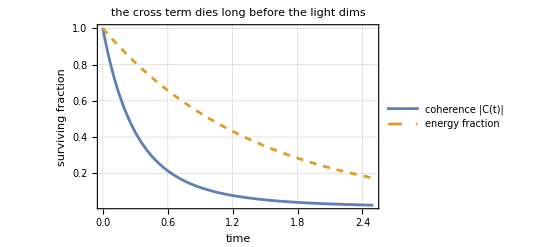

```mathematica
Plot[{Exp[-2 α0^2 (1 - Exp[-γcat t])], Exp[-γcat t]}, {t, 0, 2.5},
 PlotStyle -> {ColorData[97, 1], Directive[ColorData[97, 2], Dashed]},
 PlotLegends -> {"coherence |C(t)|", "energy fraction"}, Frame -> True, GridLines -> Automatic,
 FrameLabel -> {"time", "surviving fraction"}, PlotRange -> All,
 PlotLabel -> "the cross term dies long before the light dims"]
```

The cross term is gone while the lobes are still nearly full size: the ratio of the two rates is 2 α_0^2, and it grows with the square of the cat's size. That is the whole reason mesoscopic superpositions are fragile and macroscopic ones are hopeless.

### Turning the assumptions off

Bringing the lobes close (A4 off). The closed form never used the separation being large, so shrink it and see what actually fails. Draw the same two curves at the working size and at a small one:

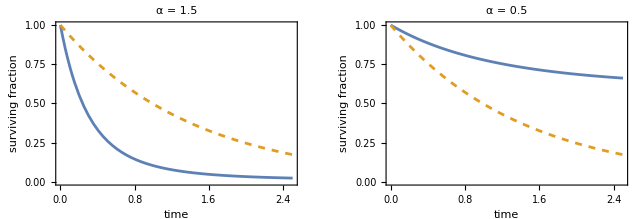

```mathematica
GraphicsRow[Table[Plot[{Exp[-2 al^2 (1 - Exp[-γcat t])], Exp[-γcat t]}, {t, 0, 2.5},
    PlotStyle -> {ColorData[97, 1], Directive[ColorData[97, 2], Dashed]}, Frame -> True,
    PlotRange -> {0, 1}, FrameLabel -> {"time", "surviving fraction"},
    PlotLabel -> Row[{"α = ", al}]], {al, {1.5, 0.5}}], ImageSize -> 640]
```

At the small size the coherence outlives a fair share of the energy: the phenomenon named in the title, decoherence far faster than dissipation, is gone. The law itself survives; confirm it by rerunning the two-route check on a small cat:

```mathematica
With[{al = 0.6},
 With[{run = evolveODE[0 blankCat, {Sqrt[γcat] downCat},
     densityMatrix[Normalize[coherentState[topCat, al] + coherentState[topCat, -al]]], 1.5]},
  Max@Table[Abs[catCoherence[run[t], al Exp[-γcat t/2]] -
      Exp[-2 al^2 (1 - Exp[-γcat t])]], {t, 0., 1.5, 0.25}]]]
```

1.08461×10^-6

Still at the solver tolerance. So A4 splits cleanly by claim: the formula for C(t) does not need it, the headline (fast decoherence) is nothing but it, and the extraction machinery degrades as the overlap grows. One assumption, three different scopes, and only the computation separates them.

Two numbers for one coherence (C1 compared). Evolve the two lobes separately, so the rival number, the trace distance between the evolved cat and the evolved even mixture of its lobes, can be computed on the same run:

```mathematica
{lobeRunA, lobeRunB} = evolveODE[0 blankCat, {Sqrt[γcat] downCat},
    densityMatrix[coherentState[topCat, #]], 2.5] & /@ {α0, -α0};
```

Plot both numbers, each normalized to its own start:

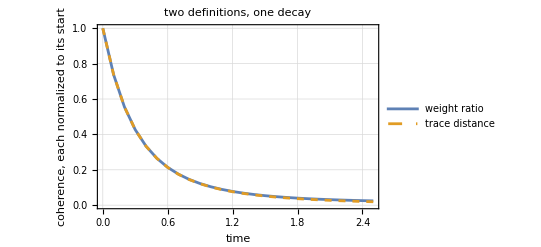

```mathematica
With[{ts = Range[0., 2.5, 0.1]},
 With[{wr = catCoherence[catRun[#], α0 Exp[-γcat #/2]] & /@ ts,
   td = traceDistance[catRun[#], (lobeRunA[#] + lobeRunB[#])/2] & /@ ts},
  ListLinePlot[{Transpose[{ts, wr/First[wr]}], Transpose[{ts, td/First[td]}]},
   PlotStyle -> {ColorData[97, 1], Directive[ColorData[97, 2], Dashed]},
   PlotLegends -> {"weight ratio", "trace distance"}, Frame -> True, GridLines -> Automatic,
   FrameLabel -> {"time", "coherence, each normalized to its start"}, PlotRange -> All,
   PlotLabel -> "two definitions, one decay"]]]
```

They lie on each other, and there is a mechanism, not luck, behind it: under this leak the evolved cat minus the evolved mixture is exactly the cross term, whose trace norm is twice its weight up to corrections of the order of the lobe overlap. So the two numbers must agree to that order while the lobes are well separated, and the agreement should degrade as they close. Measure the largest normalized gap at the working size and at the small size:

```mathematica
coherenceGap[al_, tmax_] := Module[{runC, runA, runB, ts},
   runC = evolveODE[0 blankCat, {Sqrt[γcat] downCat},
     densityMatrix[Normalize[coherentState[topCat, al] + coherentState[topCat, -al]]], tmax];
   {runA, runB} = evolveODE[0 blankCat, {Sqrt[γcat] downCat},
      densityMatrix[coherentState[topCat, #]], tmax] & /@ {al, -al};
   ts = Range[0., tmax, tmax/15];
   With[{wr = catCoherence[runC[#], al Exp[-γcat #/2]] & /@ ts,
     td = traceDistance[runC[#], (runA[#] + runB[#])/2] & /@ ts},
    Max@Abs[wr/First[wr] - td/First[td]]]];
{coherenceGap[α0, 2.5], coherenceGap[0.6, 1.5]}
```

{0.00507967,0.301378}

The first number, the well-separated gap, sits at the overlap scale; the second, the close-lobe gap, is far larger. The verdict on C1: a harmless choice inside A4's scope, a real choice outside it. A choice can inherit its innocence from an assumption, and the pairing is now on record.

A drive that rotates the lobes (A3 off). Switch on a free Hamiltonian ω (â)^†â. Phase rotation commutes with the loss dissipator, so the driven solution should be exactly the undriven one rotated in phase space, lobes at α_0 e^-iωt e^(-γt/2), with the same coherence factor. Evolve with the drive:

```mathematica
withDrive = evolveODE[1.3 numberOp[topCat], {Sqrt[γcat] downCat}, cat0, 2.5];
```

Rotate each snapshot back and measure the distance to the undriven run, the whole-state form of the claim:

```mathematica
Max@Table[With[{R = MatrixExp[-I 1.3 t numberOp[topCat]]},
   Norm[ConjugateTranspose[R] . withDrive[t] . R - catRun[t], "Frobenius"]], {t, 0.25, 2.5, 0.25}]
```

8.94263×10^-7

At the solver tolerance: the drive is a rigid rotation of the whole picture. The coherence, extracted on the rotated lobes, must then land on the same closed form:

```mathematica
Max@Table[Abs[catCoherence[withDrive[t], α0 Exp[-I 1.3 t - γcat t/2]] -
    Exp[-2 α0^2 (1 - Exp[-γcat t])]], {t, 0.25, 2.5, 0.25}]
```

1.49111×10^-7

It does. A3 is hereby deleted from the list. It was a simplification, not a load-bearing assumption: every claim above survives the drive untouched. Rule 5 cuts both ways, and this is the direction that shortens the list. The scope of the deletion is worth one sentence: what saved the claims is that a free rotation keeps coherent states coherent; a Hamiltonian that does not, a Kerr term for instance, is a genuinely different problem, and the list after the computations records the boundary that way.

A warm bath (A2 off). Give the environment a temperature: a downward channel at rate γ(n̄+1) and an upward one at rate γ n̄. Two things should happen: the answer to Q1 breaks, because a heated lobe does not stay a coherent state, and the cross term should die faster by the factor 2 n̄+1. First Q1's fate, the purity of a single evolved lobe under the warm pair:

```mathematica
purity[evolveODE[0 blankCat, {Sqrt[γcat 2.] downCat, Sqrt[γcat 1.] ConjugateTranspose[downCat]},
   densityMatrix[coherentState[topCat, α0]], 0.6][0.6]]
```

0.593153

Below one: the pointer states of the cold leak are no longer preserved, so the lobes must be evolved rather than written down. That is why the coherence here is measured by the trace distance to the evolved mixture, the C1 rival, whose innocence inside A4 was just established:

```mathematica
warmCoherence[nT_] := Module[{fall = Sqrt[γcat (nT + 1)] downCat,
    climb = Sqrt[γcat nT] ConjugateTranspose[downCat], runs},
   runs = evolveODE[0 blankCat, {fall, climb}, #, 0.6] & /@
     {cat0, densityMatrix[coherentState[topCat, α0]], densityMatrix[coherentState[topCat, -α0]]};
   Function[t, traceDistance[runs[[1]][t], (runs[[2]][t] + runs[[3]][t])/2]]];
{coldC, warmC} = {warmCoherence[0.], warmCoherence[1.]};
```

Compare the two decays, each normalized to its start:

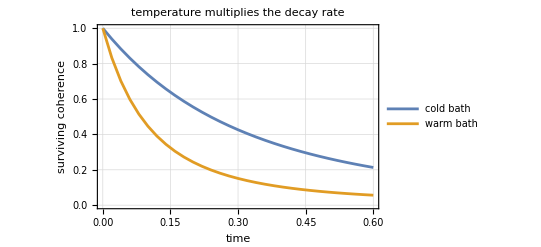

```mathematica
With[{ts = Range[0., 0.6, 0.02]},
 ListLinePlot[{Transpose[{ts, (coldC /@ ts)/coldC[0.]}], Transpose[{ts, (warmC /@ ts)/warmC[0.]}]},
  PlotStyle -> {ColorData[97, 1], ColorData[97, 2]},
  PlotLegends -> {"cold bath", "warm bath"}, Frame -> True, GridLines -> Automatic,
  FrameLabel -> {"time", "surviving coherence"}, PlotRange -> All,
  PlotLabel -> "temperature multiplies the decay rate"]]
```

The warm curve plunges. The claimed factor is 2 n̄+1; read the ratio of the early losses across a shrinking window:

```mathematica
Table[(1 - warmC[t1]/warmC[0.])/(1 - coldC[t1]/coldC[0.]), {t1, {0.04, 0.02, 0.01}}]
```

{2.54789,2.75258,2.8702}

The sequence climbs toward 2 n̄+1, which is three for this bath, as the window shrinks; the residue at finite window is the curvature of the exponential. So A2 owns the prefactor of the decoherence rate and the identity of the pointer states, while the separation-squared structure stands untouched: the catalog's Part Three works this warm case in full, and this cell is the link to it.

A bath that hands the amplitude back (A1 off). Replace the featureless environment with the smallest one that has memory: a single auxiliary mode b̂, coupled by g(â(b̂)^†+(â)^†b̂), which leaks at rate κ. The cavity amplitude then obeys a two-step chain, â feeds b̂ and b̂ feeds the void, and the transmitted amplitude u(t) obeys

u''+κ/2 u'+g^2 u=0,    u(0)=1,  u'(0)=0,

so the cavity sees a loss channel of transmissivity (u(t))^2 and the cat's coherence is exp (-2 α^2(1-(u(t))^2)). When κ≫g the auxiliary mode empties as fast as it fills, the chain forgets, and the constant rate γ_eff=4 g^2/κ returns: the assumption A1 is the statement that the bath lives in that corner. Write the amplitude and confirm it solves its equation:

```mathematica
uMode[g_, κ_][t_] := With[{om = Sqrt[g^2 - κ^2/16]},
   Exp[-κ t/4] (Cos[om t] + κ/(4 om) Sin[om t])];
FullSimplify[D[uMode[g, κ][t], {t, 2}] + (κ/2) D[uMode[g, κ][t], t] +
  g^2 uMode[g, κ][t]]
```

0

Zero identically. The memory-bath coherence in closed form:

```mathematica
memCoherence[g_, κ_, al_][t_] := Exp[-2 al^2 (1 - Re[uMode[g, κ][t]]^2)];
```

Two fingerprints separate memory from no memory. The onset: with memory the early loss is quadratic in time, 1-u^2≈g^2 t^2, where the constant-rate bath loses linearly. Compare the early coherence loss of the two, same effective rate:

```mathematica
{1 - memCoherence[1., 0.5, 1.][0.05], 1 - Exp[-2 (1 - Exp[-(4/0.5) 0.05])]}
```

{0.00496274,0.482818}

The first number, the memory bath's early loss, is a small fraction of the second: the memoried decay starts flat. And the revival: when κ<4g the amplitude swings back from the auxiliary mode before leaking, so the coherence partially returns, which no equation with a nonnegative constant rate can do. Check the closed form against the full two-mode master equation, run at a slightly smaller cat so the joint simulation stays light:

```mathematica
naMem = 9; nbMem = 9; gMem = 1.; κMem = 0.5; αMem = 1.;
aJoint = KroneckerProduct[annihilation[naMem], IdentityMatrix[nbMem]];
bJoint = KroneckerProduct[IdentityMatrix[naMem], annihilation[nbMem]];
memRun = evolveODE[gMem (aJoint . ConjugateTranspose[bJoint] + ConjugateTranspose[aJoint] . bJoint),
   {Sqrt[κMem] bJoint},
   densityMatrix[Flatten@KroneckerProduct[
      Normalize[coherentState[naMem, αMem] + coherentState[naMem, -αMem]],
      coherentState[nbMem, 0.]]], 6.];
```

Trace out the auxiliary mode and extract the cavity coherence on the transmitted lobes, sampling away from the amplitude's zero crossings where the two lobes coincide and the extraction has nothing to grip:

```mathematica
cavityOf[joint_] := TensorContract[ArrayReshape[joint, {naMem, nbMem, naMem, nbMem}], {{2, 4}}];
memSample = Select[Range[0.5, 5.75, 0.375], Abs[uMode[gMem, κMem][#]] > 0.2 &];
memDots = Table[{t, catCoherence[cavityOf[memRun[t]], αMem uMode[gMem, κMem][t]]}, {t, memSample}];
Max@Table[Abs[catCoherence[cavityOf[memRun[t]], αMem uMode[gMem, κMem][t]] -
    memCoherence[gMem, κMem, αMem][t]], {t, memSample}]
```

0.000031536

The largest gap between the two-mode simulation and the closed form is small: two routes again, one solved by hand through u(t), one a full joint master equation that never heard of u. Now draw the whole story, slow bath and fast bath, each beside the constant-rate stand-in with the same effective rate:

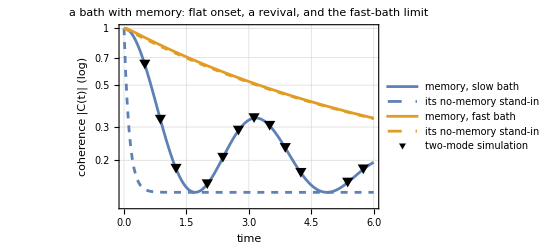

```mathematica
With[{ts = Range[0., 6., 0.04]},
 ListLogPlot[{Transpose[{ts, memCoherence[gMem, κMem, αMem] /@ ts}],
   Transpose[{ts, Exp[-2 αMem^2 (1 - Exp[-(4 gMem^2/κMem) #])] & /@ ts}],
   Transpose[{ts, memCoherence[gMem, 30., αMem] /@ ts}],
   Transpose[{ts, Exp[-2 αMem^2 (1 - Exp[-(4 gMem^2/30.) #])] & /@ ts}],
   memDots},
  Joined -> {True, True, True, True, False}, PlotMarkers -> {None, None, None, None, Automatic},
  PlotStyle -> {ColorData[97, 1], Directive[ColorData[97, 1], Dashed],
    ColorData[97, 2], Directive[ColorData[97, 2], Dashed], Black},
  PlotLegends -> {"memory, slow bath", "its no-memory stand-in",
    "memory, fast bath", "its no-memory stand-in", "two-mode simulation"},
  Frame -> True, GridLines -> Automatic, FrameLabel -> {"time", "coherence |C(t)| (log)"},
  PlotLabel -> "a bath with memory: flat onset, a revival, and the fast-bath limit"]]
```

The fast-bath pair lies together: A1 recovered as a limit. The slow-bath pair splits everywhere: the constant-rate stand-in plunges at once and stays down, while the true curve starts flat, dies, and then partially revives as the auxiliary mode hands amplitude back, with the black points from the joint simulation riding the closed form. So A1 owns the exponential time profile and the monotonicity of decoherence. What it does not own is the separation dependence: the exponent is proportional to α^2 at every instant in both columns, because that factor comes from the overlap of Gaussian lobes, not from the bath's clock. The headline's scaling needs less than the headline's curve, and this cell is, to this file's knowledge, the first in this folder to exercise the memory assumption at all.

Raising the cutoff (A5). Recompute the extracted coherence at a fixed time across three truncations:

```mathematica
With[{coherAt = Function[nn, With[{run = evolveODE[0 IdentityMatrix[nn], {Sqrt[γcat] annihilation[nn]},
       densityMatrix[Normalize[coherentState[nn, α0] + coherentState[nn, -α0]]], 0.8]},
     catCoherence[run[0.8], α0 Exp[-γcat 0.8/2]]]]},
 coherAt /@ {22, 30, 38}]
```

{0.145212,0.145212,0.145212}

The three values agree at the displayed precision: the truncation is not what any conclusion above rests on.

### The list, after the computations

The list the computations leave behind is shorter and sharper than the list we wrote. A3 is gone: a free drive rotates the picture rigidly and changes nothing, so it was never an assumption, only a simplification, with the recorded boundary that the Hamiltonian must keep coherent states coherent. A4 split into three scopes: the formula never needed it, the headline is nothing but it, and the extraction machinery fails without it. C1 turned out to be innocent exactly inside A4 and guilty outside it, so the choice of coherence number and the separation assumption travel together. A2 owns the prefactor 2 n̄+1 and the identity of the pointer states. A1 owns the exponential profile and the monotonicity, but not the separation-squared scaling, which survives even a bath that hands amplitude back. What began as five facts and a choice ends as: linearity of the loss gives the scaling, A1 gives the clock, A2 gives the prefactor, A4 gives the phenomenon.

## Part Two: Rapid Purification, Rebuilt from Its Assumptions

### The questions, weakest premises first

Q1. Does continuously watching one observable, with no drive and no feedback, purify a single monitored run? (This needs the least: one qubit, one measured channel, a kept record.)

Q2. What sets the purification rate, and can choosing what to measure, step by step, make the rate certain, the same on every record?

Q3. Is "faster" one question? Two scores are in circulation, the average impurity at a deadline and the typical time to reach a target, and nothing guarantees they rank two protocols the same way.

Q4. Which assumptions carry these answers: what changes when a drive rotates the qubit, when the detector misses a fraction of the record, when a second channel goes unwatched, when the time step is finite?

### The words, defined by computation

The qubit objects first, the Pauli matrices and the Bloch vector:

```mathematica
{id2, X, Y, Z} = Table[PauliMatrix[j], {j, 0, 3}];
blochVector[rho_] := Re[Tr[rho . #] & /@ {X, Y, Z}];
impurity[rho_] := (1 - Norm[blochVector[rho]]^2)/2;
```

Impurity is the score: ℓ=1/2(1-(a⃗)^2) for Bloch vector a⃗, one half for the maximally mixed state and zero for a pure one. It is the same information as the purity, ℓ=1-Tr ρ^2; check the identity on an arbitrary state:

```mathematica
With[{rho = {{0.7, 0.2 - 0.1 I}, {0.2 + 0.1 I, 0.3}}}, {impurity[rho], 1 - purity[rho]}]
```

{0.32,0.32}

The two numbers agree. Using impurity rather than entropy is a choice, so prove the choice harmless rather than assert it: for a qubit the von Neumann entropy is a strictly increasing function of the impurity, so the two scores rank any two states identically and reach any target in the same order:

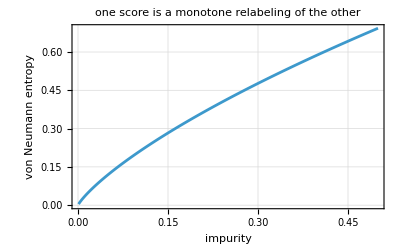

```mathematica
vnEntropy[rho_] := With[{ev = Select[Re@Eigenvalues[N@rho], # > 10^-12 &]}, -Total[ev Log[ev]]];
ListLinePlot[Table[{(1 - r^2)/2, vnEntropy[(id2 + r Z)/2]}, {r, 0.999, 0.001, -0.002}],
 Frame -> True, GridLines -> Automatic, FrameLabel -> {"impurity", "von Neumann entropy"},
 PlotLabel -> "one score is a monotone relabeling of the other"]
```

```mathematica
With[{vals = Table[vnEntropy[(id2 + r Z)/2], {r, 0.999, 0.001, -0.002}]},
 Min[Differences[vals]] > 0]
```

True

Monotone, confirmed. Purifies, though, is the word that genuinely needs pinning, because it has at least three inequivalent meanings: (i) pathwise, every single run's impurity goes to zero; (ii) in the mean, the ensemble-averaged impurity falls; (iii) in passage, the time to first reach a chosen impurity is short. The development below computes all three and shows they come apart: (i) and (ii) disagree about whether an unmonitored qubit purifies at all, and (ii) and (iii) reverse the ranking of two protocols. Faster inherits the same ambiguity, and Q3 is the demonstration.

Measurement strength is a convention to declare, not discover: the monitored observable M̂ enters as the channel ĉ=√k M̂, and the record increment in this convention is dJ=2 √k ⟨M̂⟩ dt+dW with a Wiener increment dW of variance dt.

Steered means one thing only: the record chooses the next measured axis. No Hamiltonian is ever applied to the qubit; the feedback loop closes through the choice of observable, and the step function below shows it, one measurement update per step and nothing else.

### The assumptions

B1, a fact, held provisionally: nothing drives the qubit. No Hamiltonian between measurements. Turned off under Switch the drive on, and partially demoted there.

B2, a fact: the detector is perfect. Every bit of the record is kept, efficiency η=1. Turned off under A detector that misses, where the verdict between the two protocols reverses.

B3, a fact: the measured channel is the only channel. Nothing else couples to the qubit. Turned off under A second channel, unwatched.

B4, numerical: a finite step stands in for continuous monitoring. Refined inside the development, where the deterministic claim is tested against the step size.

C2, a choice: the score is impurity. Proven equivalent to entropy above. C3, a choice: the strength convention stated above.

### From watching to steering, and what faster means

The conditioned state under a monitored channel needs a positivity-preserving update; this is the structure-preserving step of Rouchon and Ralph, exactly as the catalog builds it:

```mathematica
measurementStep[H_, watched_, effs_, unwatched_, dt_] := Enclose[
  Module[{d = Length[H], id = IdentityMatrix[Length[H]], channels = Join[watched, unwatched], drift, corr},
   ConfirmAssert[VectorQ[effs, 0 <= # <= 1 &], "efficiencies must lie in [0,1]"];
   ConfirmAssert[TrueQ[dt > 0], "time step must be positive"];
   drift = I H + Fold[Plus, 0 H, ConjugateTranspose[#] . # & /@ channels]/2;
   corr = Fold[Plus, 0 H, MapThread[#1 (#2 . #2) &, {effs, watched}]]/2;
   Function[{rho, dJ}, Module[{sig, M, top, nrm},
     sig = Fold[Plus, 0 H, MapThread[Sqrt[#2] #1 #3 &, {dJ, effs, watched}]];
     M = id - drift dt + sig + sig . sig/2 - corr dt;
     top = M . rho . ConjugateTranspose[M] +
       dt Fold[Plus, 0 H, # . rho . ConjugateTranspose[#] & /@ unwatched] +
       dt Fold[Plus, 0 H, MapThread[(1 - #2) #1 . rho . ConjugateTranspose[#1] &, {watched, effs}]];
     nrm = Re@Tr[top];
     If[TrueQ[nrm > 0], top/nrm,
       Failure["NonPositiveNormalization", <|"Normalization" -> nrm|>]]]]]];
```

The record model and one full monitored trajectory, states and record together:

```mathematica
measurementRecord[rho_, watched_List, effs_List, dt_, kick_List] :=
  MapThread[Sqrt[#3] Re@Tr[(#1 + ConjugateTranspose[#1]) . rho] dt + #2 &,
   {watched, kick, effs}];
trajectory[rho0_, H_, watched_List, effs_List, unwatched_List, dt_, tf_, seed_] :=
  BlockRandom[SeedRandom[seed];
   Module[{n = Round[tf/dt], step, kicks, states, record},
    step = measurementStep[H, watched, effs, unwatched, dt];
    kicks = RandomVariate[NormalDistribution[0, Sqrt[dt]], {n, Length[watched]}];
    states = FoldList[
      Function[{r, dw}, step[r, measurementRecord[r, watched, effs, dt, dw]]], rho0, kicks];
    record = MapThread[measurementRecord[#1, watched, effs, dt, #2] &, {Most[states], kicks}];
    <|"times" -> dt Range[0, n], "states" -> states, "record" -> record|>]];
```

Q1. Fix the strength and the step, start maximally mixed, watch a fixed axis, and follow the impurity of five runs:

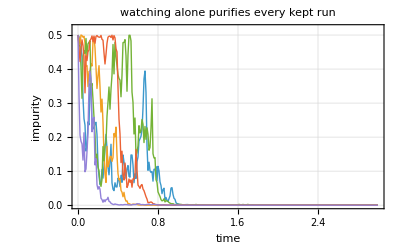

```mathematica
kPur = 1.; hPur = 0.01;
With[{runs = Table[impurity /@ trajectory[id2/2, 0 id2, {Sqrt[kPur] Z}, {1.}, {}, hPur, 3., s]["states"], {s, 5}]},
 ListLinePlot[Transpose[{hPur Range[0, 300], #}] & /@ runs,
  Frame -> True, GridLines -> Automatic, PlotStyle -> Thick, PlotRange -> {0, 0.52},
  FrameLabel -> {"time", "impurity"}, PlotLabel -> "watching alone purifies every kept run"]]
```

Every run falls toward zero: watching purifies in the pathwise sense. In the mean sense the unconditioned qubit does not purify at all, since averaging the conditioned states over records returns the maximally mixed steady state; purification is a property of runs, not of the average, the first place the meanings of "purifies" separate. This uses B2 and B3; the rate it happens at is the next question.

Q2. Write the impurity's increment under monitoring of an axis at angle θ_t to the Bloch vector,

d ℓ_t=-4k ℓ_t(sin^2 θ_t+2 ℓ_t cos^2 θ_t)dt-4 √k ℓ_t √(1-2 ℓ_t) cos θ_t d W_t.

The noise rides on cos θ_t. A fixed axis lets the sharpening state drift into alignment, θ_t→0, where the drift is weakest and the noise largest; holding θ_t=π/2 kills the noise term outright and leaves the deterministic law ℓ_t=ℓ_0 e^(-4kt) on every record. Holding the angle takes re-aiming, and the re-aiming is the steering: read the state, measure perpendicular to it, repeat. The step is the same measurement update; only the axis moves, and an efficiency argument is carried for later:

```mathematica
steered[rho0_, H_, k_, eta_, h_, tf_, seed_] := BlockRandom[SeedRandom[seed];
   Module[{n = Round[tf/h], perp},
    perp[a_] := With[{c = Cross[a, {0, 0, 1.}]}, If[Norm[c] < 1.*^-6, {1., 0., 0.}, Normalize[c]]];
    FoldList[Function[{rho, dw},
      With[{leak = Sqrt[k] (perp[blochVector[rho]] . {X, Y, Z})},
       measurementStep[H, {leak}, {eta}, {}, h][rho, measurementRecord[rho, {leak}, {eta}, h, {dw}]]]],
     rho0, RandomVariate[NormalDistribution[0, Sqrt[h]], n]]]];
```

Overlay thirty steered runs on the closed law, on a log scale where the law is a straight line:

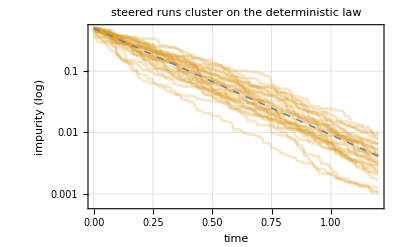

```mathematica
With[{runs = Table[impurity /@ steered[id2/2, 0 id2, kPur, 1., hPur, 1.2, s], {s, 30}],
  grid = hPur Range[0, 120]},
 ListLogPlot[Append[Transpose[{grid, #}] & /@ runs, Transpose[{grid, 0.5 Exp[-4 kPur grid]}]],
  Joined -> True,
  PlotStyle -> Append[ConstantArray[Directive[ColorData[97, 2], Opacity[0.25]], 30],
    Directive[Thick, ColorData[97, 1], Dashed]],
  Frame -> True, GridLines -> Automatic, FrameLabel -> {"time", "impurity (log)"},
  PlotLabel -> "steered runs cluster on the deterministic law"]]
```

The runs hug the dashed line with a small scatter. The law is route one; the simulation is route two; and B4 says the scatter should be the step's fault, not physics. Test that: at a fixed physical time, refine the step and watch both the spread across runs and the distance to the law contract:

```mathematica
TableForm[
 Table[With[{fin = Table[Last[impurity /@ steered[id2/2, 0 id2, kPur, 1., h, 0.6, s]], {s, 60}],
    target = 0.5 Exp[-4 kPur 0.6]},
   {h, Mean[fin], StandardDeviation[fin], Abs[Mean[fin] - target]}],
  {h, {0.02, 0.01, 0.005}}],
 TableHeadings -> {None, {"step h", "mean impurity", "spread", "gap to the law"}}]
```

step h | mean impurity | spread | gap to the law
0.02 | 0.0551601 | 0.0299066 | 0.00980115
0.01 | 0.0533276 | 0.0213267 | 0.00796867
0.005 | 0.0481931 | 0.0138 | 0.00283416

Both columns shrink with the step: the determinism is a property of the continuous limit, and the finite-step residue converges to it. B4 is exercised and behaves.

Q3. Now the word "faster," split into its two scores on the same two ensembles, a fixed-axis one and a steered one, over a window long enough for every run to reach the target:

```mathematica
unsteeredEns = Table[impurity /@ trajectory[id2/2, 0 id2, {Sqrt[kPur] Z}, {1.}, {}, hPur, 4., s]["states"], {s, 150}];
steeredEns = Table[impurity /@ steered[id2/2, 0 id2, kPur, 1., hPur, 4., s], {s, 150}];
```

For the passage score, record each run's first time below a target impurity, leaving a run that never crosses explicitly marked rather than silently scored at the window's end, and count the marks before averaging anything:

```mathematica
firstPassage[run_] := With[{pos = FirstPosition[run, l_ /; l < 0.05]},
   If[MissingQ[pos], Missing["RightCensored"], (First[pos] - 1) hPur]];
{fptU, fptS} = {firstPassage /@ unsteeredEns, firstPassage /@ steeredEns};
{Count[fptU, _Missing], Count[fptS, _Missing]}
```

{0,0}

The pair of counts, fixed-axis then steered, comes back zero: every run crossed, so the plain means below are unbiased. Compare the two scores head to head:

```mathematica
Grid[{{"", "fixed axis", "steered"},
  {"mean impurity at t = 0.6", Mean[unsteeredEns[[All, 61]]], Mean[steeredEns[[All, 61]]]},
  {"mean first-passage time to impurity 0.05", Mean[fptU], Mean[fptS]}},
 Frame -> All, Alignment -> Left]
```

| fixed axis | steered
mean impurity at t = 0.6 | 0.0869488 | 0.0530162
mean first-passage time to impurity 0.05 | 0.476467 | 0.6046

The two rows disagree about the winner: steering gives the lower impurity at the deadline, and the fixed axis gives the shorter mean time to the target. The distributions say why:

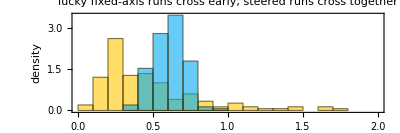

```mathematica
Histogram[{fptU, fptS}, {0, 2., 0.1}, "PDF",
 ChartLegends -> {"fixed axis", "steered"}, Frame -> True, AspectRatio -> 1/3,
 FrameLabel -> {"first-passage time to impurity 0.05", "density"},
 PlotLabel -> "lucky fixed-axis runs cross early; steered runs cross together"]
```

The fixed-axis times spread wide, with a lucky early crowd and a slow tail; the steered times bunch at one value, because determinism forbids luck in both directions. So Q3's answer: "which is faster" is not one question. Under the deadline score steering wins; under the race score the fixed axis wins; and any essay claiming one protocol "purifies faster" without naming its score has not said anything yet. This is the same lesson as Gaussian versus thermal, now about an adverb.

### Turning the assumptions off

Switch the drive on (B1 off). Add a Hamiltonian Ω/2(σ̂)_x and rerun both protocols. For the steered one nothing should change: the re-aiming reads the state after each step, so a known rotation between steps is absorbed by the next choice of axis, and the deterministic law should survive. For the fixed axis the drive should help: the slow tail came from runs stuck aligned with the measured axis, and a rotation keeps pulling the state away from alignment, where the measurement learns fastest. First the fixed axis, driven against undriven, with the steered mean for scale:

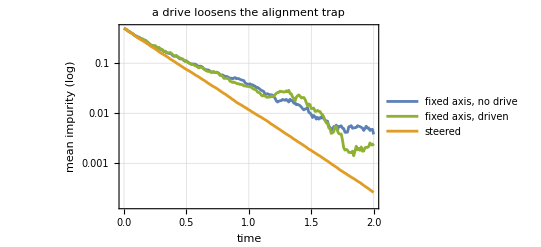

```mathematica
With[{grid = hPur Range[0, 200],
  meanDrive = Mean[Table[impurity /@ trajectory[id2/2, (1.5/2) X, {Sqrt[kPur] Z}, {1.}, {}, hPur, 2., s]["states"], {s, 100}]]},
 ListLogPlot[{Transpose[{grid, Take[Mean[unsteeredEns], 201]}], Transpose[{grid, meanDrive}],
   Transpose[{grid, Take[Mean[steeredEns], 201]}]},
  Joined -> True, PlotStyle -> {ColorData[97, 1], ColorData[97, 3], ColorData[97, 2]},
  PlotLegends -> {"fixed axis, no drive", "fixed axis, driven", "steered"},
  Frame -> True, GridLines -> Automatic, FrameLabel -> {"time", "mean impurity (log)"},
  PlotLabel -> "a drive loosens the alignment trap"]]
```

The driven fixed axis falls between the two: the rotation keeps pulling the state off the measured axis, undoing part of the alignment trap, though far from all of it. Now the steered protocol with the same drive, its ensemble mean at a fixed time beside the undriven ensemble at the same step and the continuum law:

```mathematica
With[{finDriven = Table[Last[impurity /@ steered[id2/2, (1.5/2) X, kPur, 1., hPur, 0.6, s]], {s, 60}],
  finFree = Table[Last[impurity /@ steered[id2/2, 0 id2, kPur, 1., hPur, 0.6, s]], {s, 60}]},
 {Mean[finDriven], Mean[finFree], 0.5 Exp[-4 kPur 0.6]}]
```

{0.0533461,0.0533276,0.045359}

The driven and undriven means coincide, and both carry the same small finite-step offset from the law, the offset the refinement table already charged to the step: the drive contributed nothing, so the steered claim never needed B1. B1 is demoted, with a scope split: for the steered headline it was no assumption at all, while for the fixed-axis baseline it was load-bearing, since its characteristic slowness was the alignment trap that a drive partly unmakes. The strong-drive, strong-measurement competition in its own right is the catalog's quantum Zeno section; this cell is the link to it.

A detector that misses (B2 off). Let the detector keep a fraction η of the record. The steered protocol holds the state perpendicular to the measured axis, which is exactly where the unrecorded fraction of the measurement, acting as dephasing about that axis, bites hardest; at the held angle the deterministic part of the increment becomes dℓ=2k(1-2ℓ) dt-2ηk dt, back-action heating against recorded information, which balances at the floor

ℓ_⋆=(1-η)/2,

and at η=1 collapses back to the pure-state law. The fixed axis has no such floor: its destinations are the measured observable's eigenstates, which the unrecorded dephasing cannot touch, so every run still ends pure, only later. Run both at the same imperfect efficiency:

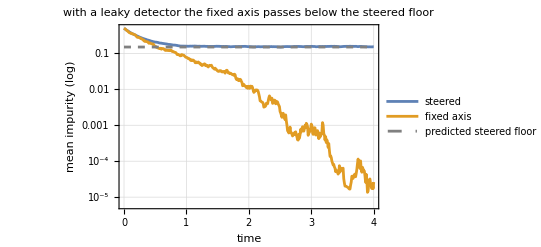

```mathematica
etaPur = 0.7;
steeredEta = Table[impurity /@ steered[id2/2, 0 id2, kPur, etaPur, hPur, 4., s], {s, 80}];
unsteeredEta = Table[impurity /@ trajectory[id2/2, 0 id2, {Sqrt[kPur] Z}, {etaPur}, {}, hPur, 4., s]["states"], {s, 80}];
With[{grid = hPur Range[0, 400]},
 ListLogPlot[{Transpose[{grid, Mean[steeredEta]}], Transpose[{grid, Mean[unsteeredEta]}],
   Transpose[{grid, ConstantArray[(1 - etaPur)/2, Length[grid]]}]},
  Joined -> True, PlotStyle -> {ColorData[97, 1], ColorData[97, 2], Directive[Gray, Dashed]},
  PlotLegends -> {"steered", "fixed axis", "predicted steered floor"},
  Frame -> True, GridLines -> Automatic, FrameLabel -> {"time", "mean impurity (log)"},
  PlotLabel -> "with a leaky detector the fixed axis passes below the steered floor"]]
```

Confirm the floor quantitatively, late steered mean against the prediction:

```mathematica
{Mean[Last /@ steeredEta], (1 - etaPur)/2}
```

{0.152573,0.15}

The pair agrees. B2 is load-bearing, and turning it off reverses the verdict at long times: the steered protocol, unbeatable at early deadlines, saturates at a floor set by the missing record, while the fixed axis crosses below that floor and keeps going, because it drives the state to destinations immune to the noise the lost record leaves behind. A protocol optimized for the ideal assumption pays rent on it forever.

A second channel, unwatched (B3 off). The channel to open matters, and choosing it is itself an exercise in reading attractors: an unwatched decay would not do, because its own destination is the pure ground state, so every run would still end pure, only later and for a different reason. To cap purity the unwatched door must lead somewhere mixed. Open the warm pair from part one's A2, downward at rate γ(n̄+1) and upward at γ n̄, here with γ=0.4 and n̄=1, beside the watched axis:

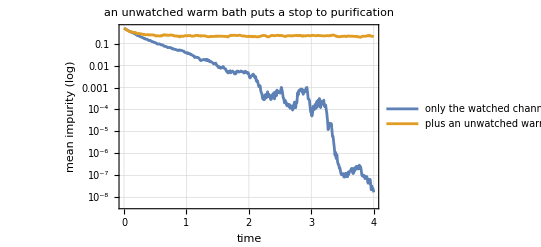

```mathematica
With[{grid = hPur Range[0, 400],
  lossy = Mean[Table[impurity /@ trajectory[id2/2, 0 id2, {Sqrt[kPur] Z}, {1.},
       {Sqrt[0.8] (X - I Y)/2, Sqrt[0.4] (X + I Y)/2}, hPur, 4., s]["states"], {s, 80}]]},
 ListLogPlot[{Transpose[{grid, Mean[unsteeredEns]}], Transpose[{grid, lossy}]},
  Joined -> True, PlotStyle -> {ColorData[97, 1], ColorData[97, 2]},
  PlotLegends -> {"only the watched channel", "plus an unwatched warm pair"},
  Frame -> True, GridLines -> Automatic, FrameLabel -> {"time", "mean impurity (log)"},
  PlotLabel -> "an unwatched warm bath puts a stop to purification"]]
```

With the warm pair open the mean impurity stops falling and holds at a working level: information now leaves through doors the record does not cover, and no choice of measured axis closes them. Purity is a property of the record kept, not of the watching; the catalog's driven-atom section carries this to its full conclusion, three levels of record on one atom, and this cell is the link to it, as it is to part one's warm bath.

### The list, after the computations

B1 is demoted with a split scope: irrelevant to the steered headline, load-bearing for the fixed-axis baseline it is compared against. B2 is load-bearing twice over: it sets the steered floor (1-η)/2, and its failure reverses which protocol wins at long times, a reversal invisible in every ideal-detector account. B3 is load-bearing with a twist the computation forced: an unwatched channel caps purity only when its own attractor is mixed, so even turning an assumption off required reading a fixed point first. B4 was never physics: the deterministic law belongs to the continuum, and the finite step converges to it on refinement. The choices came out clean: the score (C2) is a monotone relabeling of entropy, and the convention (C3) was declared once and used throughout. And the two scores hiding inside the word "faster" rank the protocols oppositely, which is not an assumption at all but a definition, the kind Rule 2 exists to catch.

## Where This Leaves the Method

Two systems, one skeleton. In each part the questions came before the machinery, every weight-carrying word acquired a computation that answers yes or no, the assumption list was written down and then made to fight for its entries, and the headline claim was reached along two routes that share no code. The lists did not survive contact intact, and that is the point: a drive assumption died in each part, a scope split three ways in one and two ways in the other, a detector assumption turned out to decide which protocol wins, and one bath assumption owned a curve's shape but not its scaling. None of that is visible in a governing equation stated whole; all of it is one turning-off cell away. The same skeleton fits any system in the catalog next door, and the cost is bounded: a few definition cells, a list, and one honest computation per entry.